# Computational Discrete Mathematics: Combinatorics and Graph Theory with Mathematica

## 1. Combinatorica : An Explorer' s Guide

```mathematica
Needs["Combinatorica`"]
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

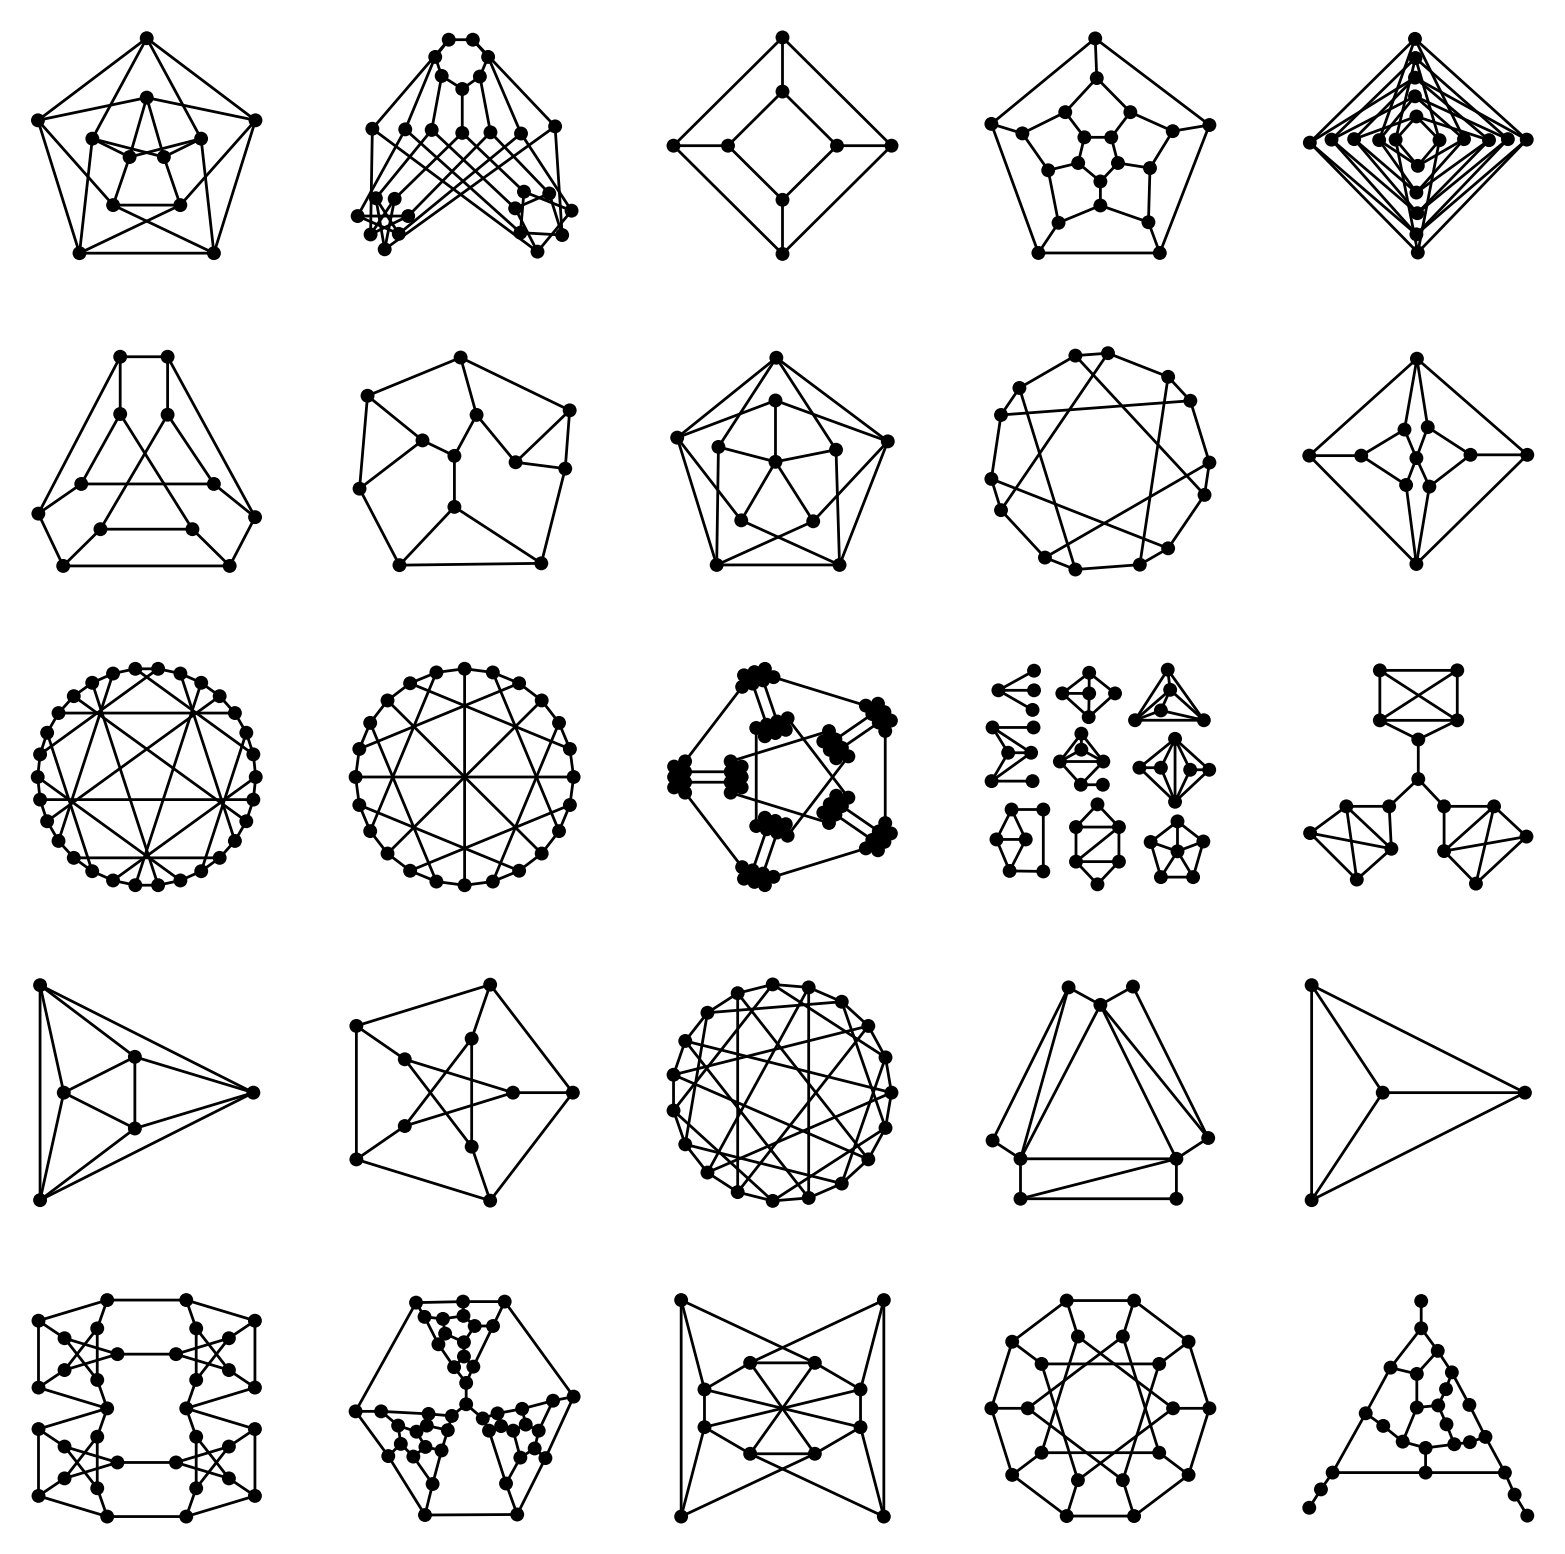

```mathematica
ShowGraphArray[Partition[FiniteGraphs,5]]
```

## 1.1 Combinatorial Objects: Permutations, Subsets, Partitions

### 1.1.1 Permutations and Subsets

```mathematica
Permutations[3]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

```mathematica
Combinatorica`Permute[{a,b,c,d},Permutations[3]]
```

{{a,b,c},{a,c,b},{b,a,c},{b,c,a},{c,a,b},{c,b,a}}

```mathematica
Permute[{5,2,4,3,1},InversePermutation[{5,2,4,3,1}]]
```

{1,2,3,4,5}

```mathematica
MinimumChangePermutations[{a,b,c}]
```

{{a,b,c},{b,a,c},{c,a,b},{a,c,b},{b,c,a},{c,b,a}}

```mathematica
RankPermutation[{8,9,7,1,6,4,5,3,2}]
```

321953

```mathematica
UnrankPermutation[321953,9]
```

{8,9,7,1,6,4,5,3,2}

```mathematica
Table[RandomPermutation[3],{20}]
```

{{2,1,3},{1,3,2},{3,1,2},{3,1,2},{2,1,3},{3,2,1},{3,1,2},{2,3,1},{3,2,1},{3,1,2},{2,3,1},{1,2,3},{1,2,3},{1,3,2},{3,2,1},{3,2,1},{2,3,1},{2,1,3},{2,1,3},{3,2,1}}

```mathematica
p=RandomPermutation[10];{p,ToCycles[p]}
```

{{2,3,5,1,7,8,10,4,9,6},{{2,3,5,7,10,6,8,4,1},{9}}}

```mathematica
NecklacePolynomial[6,{a,b,c},Cyclic]
```

a^6+a^5 b+3 a^4 b^2+4 a^3 b^3+3 a^2 b^4+a b^5+b^6+a^5 c+5 a^4 b c+10 a^3 b^2 c+10 a^2 b^3 c+5 a b^4 c+b^5 c+3 a^4 c^2+10 a^3 b c^2+16 a^2 b^2 c^2+10 a b^3 c^2+3 b^4 c^2+4 a^3 c^3+10 a^2 b c^3+10 a b^2 c^3+4 b^3 c^3+3 a^2 c^4+5 a b c^4+3 b^2 c^4+a c^5+b c^5+c^6

```mathematica
NecklacePolynomial[6,{a,b,c},Cyclic]/.{a->1,b->1,c->1}
```

130

```mathematica
NecklacePolynomial[6,{a,b,c},Cyclic]/.{a|b|c->1}
```

130

```mathematica
(p=RandomPermutation[50];{Inversions[p],Inversions[InversePermutation[p]]})
```

{686,686}

```mathematica
System`Subsets[{1,2,3,4}]
```

{{},{1},{2},{3},{4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4},{1,2,3,4}}

```mathematica
Combinatorica`Subsets[{1,2,3,4}]
```

Subsets[{1,2,3,4}]

```mathematica
KSubsets[{1,2,3,4,5},3]
```

{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5}}

```mathematica
System`Subsets[{1,2,3,4,5},{3}]
```

{{1,2,3},{1,2,4},{1,2,5},{1,3,4},{1,3,5},{1,4,5},{2,3,4},{2,3,5},{2,4,5},{3,4,5}}

```mathematica
MultiplicationTable[{1,2,3},Times]
```

{{1,2,3},{2,0,0},{3,0,0}}

### Section 1.1.2 Partitions, Compositions, and Young Tableaux

```mathematica
Partitions[6]
```

{{6},{5,1},{4,2},{4,1,1},{3,3},{3,2,1},{3,1,1,1},{2,2,2},{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}

```mathematica
Table[Length[Partitions[i]],{i,20}]
```

{1,2,3,5,7,11,15,22,30,42,56,77,101,135,176,231,297,385,490,627}

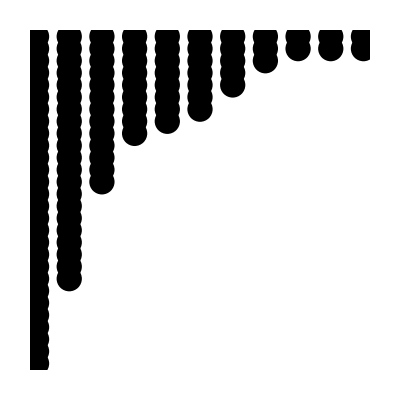

```mathematica
FerrersDiagram[RandomPartition[100]]
```

```mathematica
Compositions[5,3]
```

{{0,0,5},{0,1,4},{0,2,3},{0,3,2},{0,4,1},{0,5,0},{1,0,4},{1,1,3},{1,2,2},{1,3,1},{1,4,0},{2,0,3},{2,1,2},{2,2,1},{2,3,0},{3,0,2},{3,1,1},{3,2,0},{4,0,1},{4,1,0},{5,0,0}}

```mathematica
SetPartitions[3]
```

{{{1,2,3}},{{1},{2,3}},{{1,2},{3}},{{1,3},{2}},{{1},{2},{3}}}

```mathematica
Tableaux[{2,2,1}]
```

{{{1,4},{2,5},{3}},{{1,3},{2,5},{4}},{{1,2},{3,5},{4}},{{1,3},{2,4},{5}},{{1,2},{3,4},{5}}}

```mathematica
Tableaux[3]
```

{{{1,2,3}},{{1,3},{2}},{{1,2},{3}},{{1},{2},{3}}}

```mathematica
NumberOfTableaux[10]
```

9496

```mathematica
NumberOfTableaux[20]
```

23758664096

```mathematica
TableForm[RandomTableau[{6,5,5,4,3,2}]]
```

1 | 3 | 4 | 10 | 14 | 17
2 | 5 | 12 | 13 | 20 | 
6 | 8 | 15 | 19 | 22 | 
7 | 9 | 18 | 25 |  | 
11 | 21 | 23 |  |  | 
16 | 24 |  |  |  |

```mathematica
p=RandomPermutation[7^2+1];
Map[Length[LongestIncreasingSubsequence[#]]&,{p,Reverse[p]}]
```

{11,12}

## 1.2 Graph Theory and Algorithms

### 1.2.1 Representing Graphs

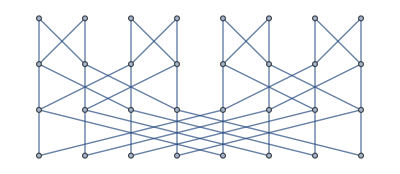

```mathematica
System`ButterflyGraph[3]
```

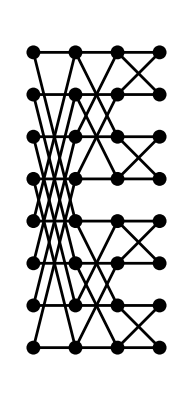

```mathematica
ShowGraph[Combinatorica`ButterflyGraph[3]]
```

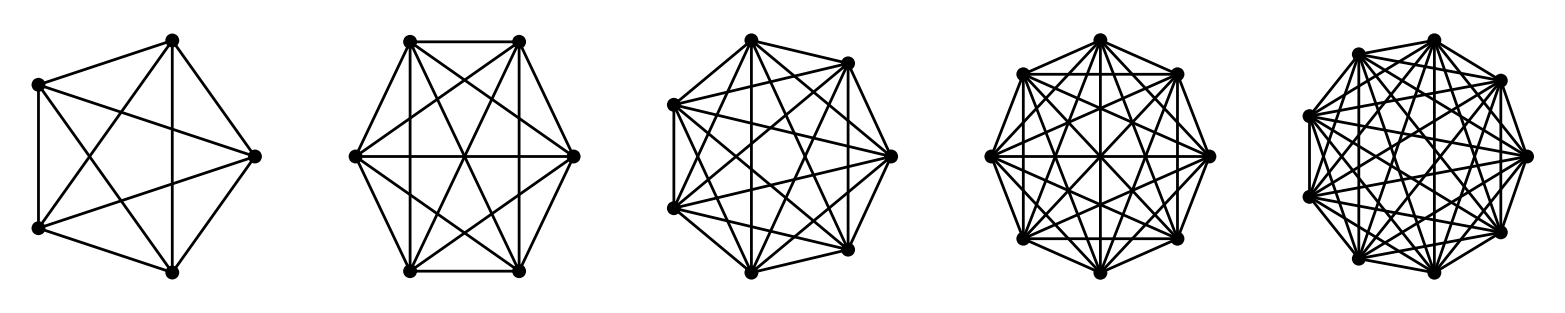

```mathematica
ShowGraphArray[Table[CompleteGraph[n],{n,5,9}]]
```

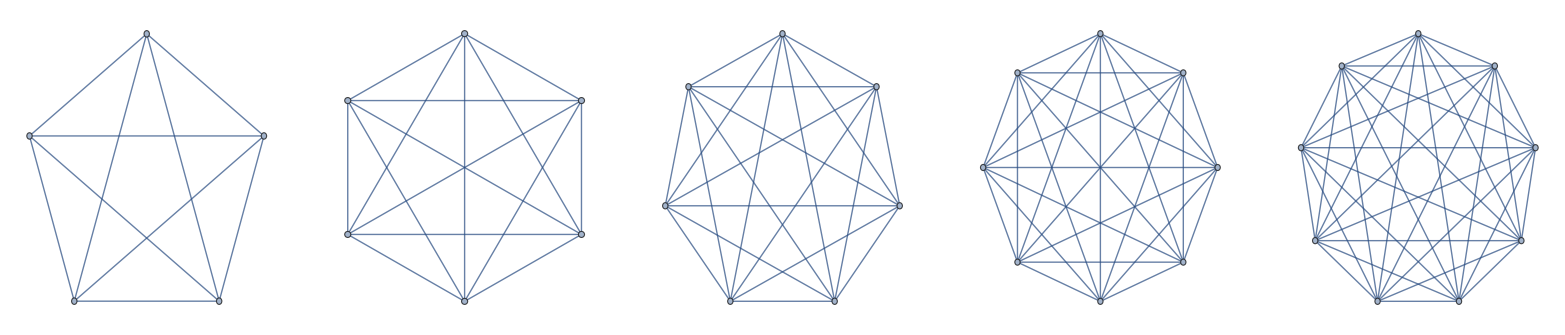

```mathematica
GraphicsRow@Table[System`CompleteGraph[n],{n,5,9}]
```

```mathematica
System`RandomTree[20]
```

-Graphics-

```mathematica
Vertices[ButterflyGraph[2]]
```

{{1.,-1.5},{2.,-1.5},{3.,-1.5},{1.,-0.5},{2.,-0.5},{3.,-0.5},{1.,0.5},{2.,0.5},{3.,0.5},{1.,1.5},{2.,1.5},{3.,1.5}}

```mathematica
VertexList[System`ButterflyGraph[2]]
```

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
V[Hypercube[4]]
```

16

```mathematica
M[CompleteGraph[5]]
```

10

```mathematica
g=SetGraphOptions[CompleteGraph[4],VertexColor->Red,EdgeColor->Blue]
```

⁃Graph:<6,4,Undirected>⁃

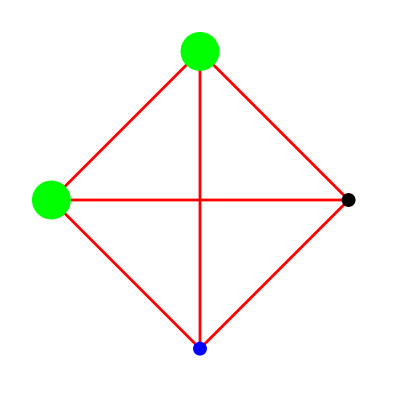

```mathematica
ShowGraph[g=SetGraphOptions[CompleteGraph[4],{{1,2,VertexColor->Green,VertexStyle->Disk[Large]},{3,VertexColor->Blue}},EdgeColor->Red]]
```

```mathematica
Vertices[g,All]
```

{{{0,1.},VertexColor→RGBColor[0, 1, 0],VertexStyle→Disk[Large]},{{-1.,0},VertexColor→RGBColor[0, 1, 0],VertexStyle→Disk[Large]},{{0,-1.},VertexColor→RGBColor[0, 0, 1]},{{1.,0}}}

```mathematica
GraphOptions[g]
```

{EdgeColor→RGBColor[1, 0, 0]}

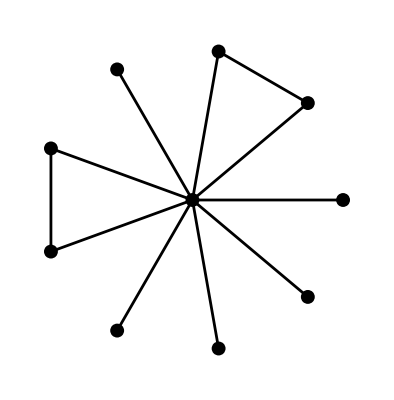

```mathematica
ShowGraph[AddEdges[Star[10],{{1,2},{4,5}}]]
```

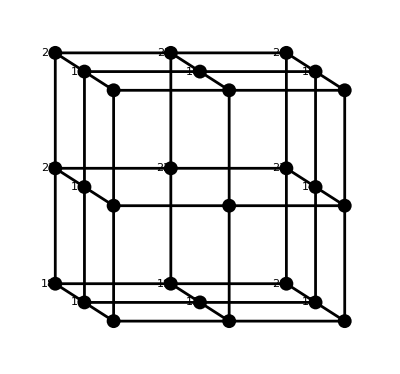

```mathematica
ShowGraph[DeleteVertices[GridGraph[3,3,3],{14}],VertexNumber->True]
```

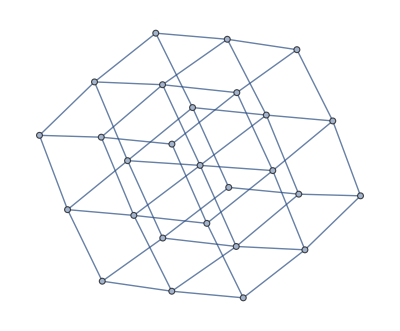

```mathematica
System`GridGraph[{3,3,3}]
```

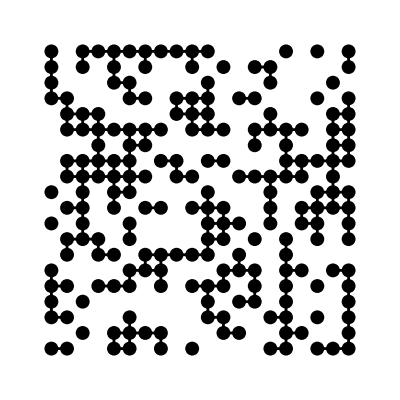

```mathematica
ShowGraph[InduceSubgraph[GridGraph[20,20],RandomSubset[Range[400]]]]
```

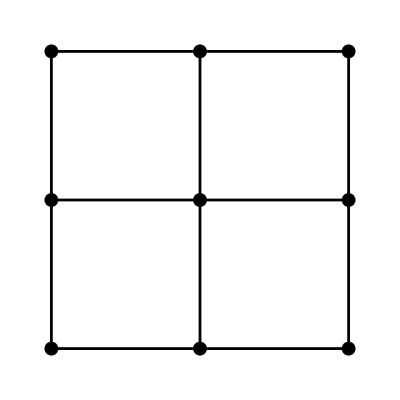

```mathematica
ShowGraph[GridGraph[3,3]]
```

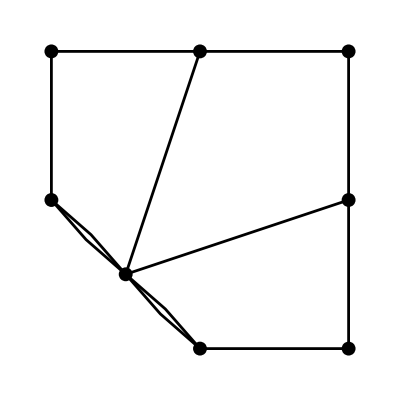

```mathematica
ShowGraph[g=Contract[GridGraph[3,3],{1,5}]]
```

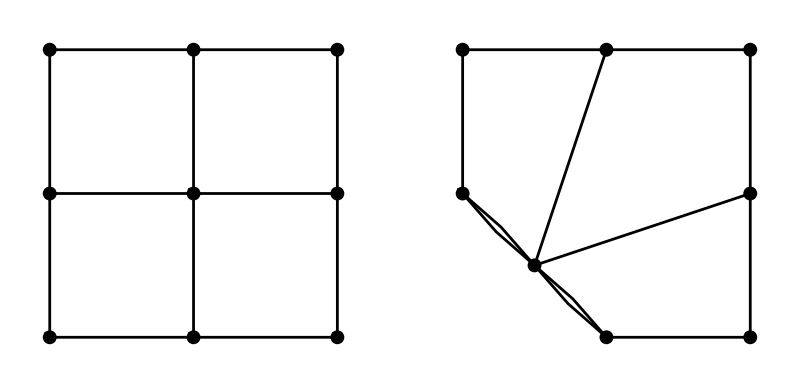

```mathematica
ShowGraphArray[{GridGraph[3,3],Contract[GridGraph[3,3],{1,5}]},VertexNumber->True]
```

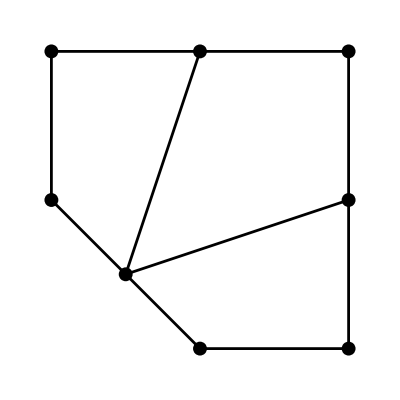

```mathematica
ShowGraph[MakeSimple[g]]
```

```mathematica
(m=ToAdjacencyMatrix[g])//TableForm
```

ToAdjacencyMatrix[RandomTree[6]]

```mathematica
EdgeList[g=System`RandomTree[6]]
```

{{4,{2}}->{5,{2,1}},{4,{2}}->{6,{2,2}},{3,{}}->{2,{1}},{3,{}}->{4,{2}},{3,{}}->{1,{3}}}

### 1.2.2 Drawing Graphs

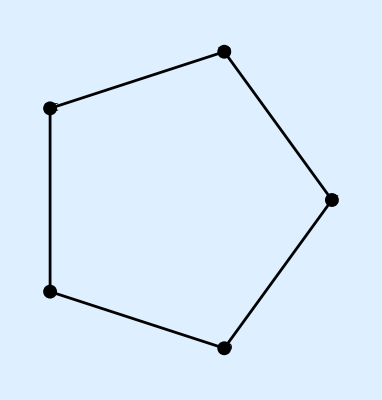

```mathematica
ShowGraph[Cycle[5],VertexNumber->True,VertexLabel->{"B","C","A","D","E"},Background->LightBlue]
```

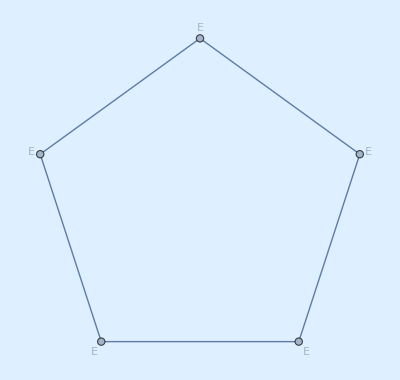

```mathematica
Show[System`CycleGraph[5,VertexLabels->{"B","C","A","D","E"}],Background->LightBlue]
```

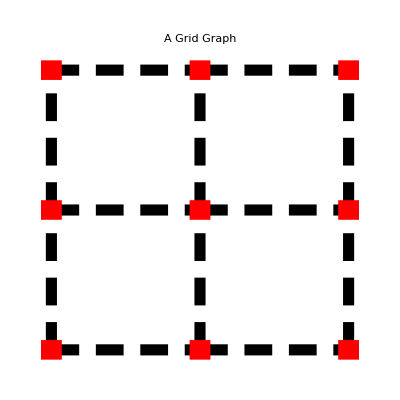

```mathematica
ShowGraph[GridGraph[3,3],VertexStyle->Box[Large],EdgeStyle->ThickDashed,VertexColor->Red,PlotLabel->"A Grid Graph",TextStyle->{FontSize->12}]
```

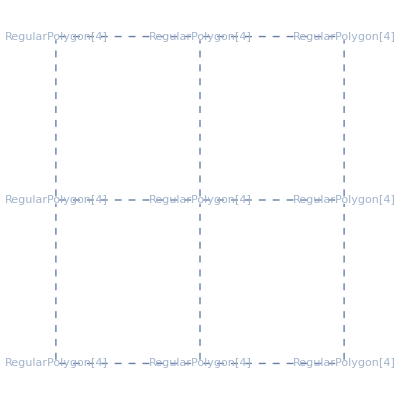

```mathematica
System`GridGraph[{3,3},System`EdgeStyle->{Thick,Dashed},System`VertexShape->RegularPolygon[4]]
```

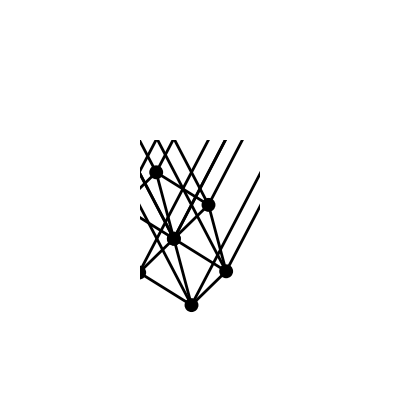

```mathematica
ShowGraph[Combinatorica`Hypercube[5],PlotRange->Zoom[{1,2,3,4}],VertexNumber->True,LabelStyle->{FontSize->14}]
```

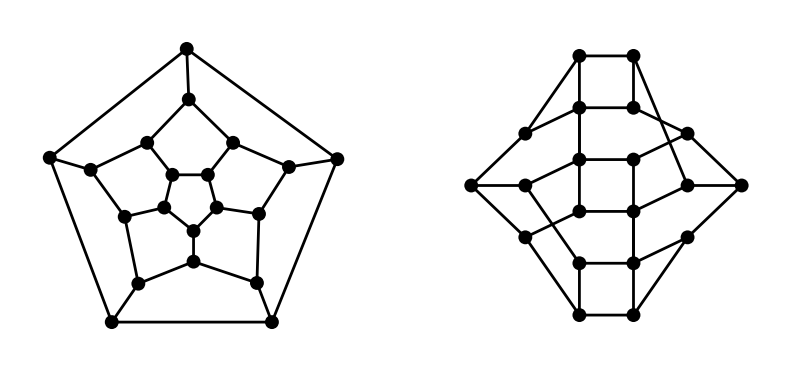

```mathematica
ShowGraphArray[{g=DodecahedralGraph,RankedEmbedding[g,{3}]}]
```

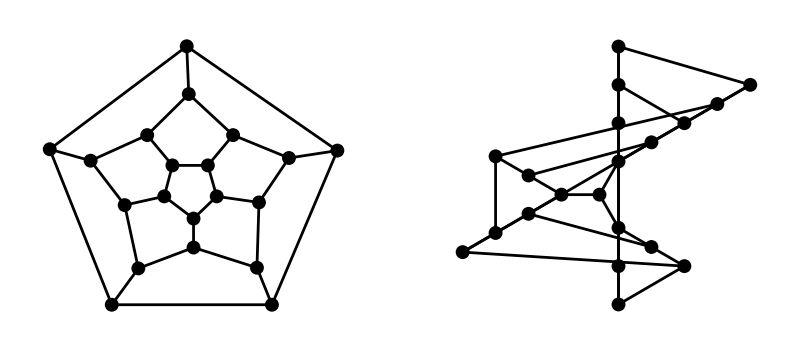

```mathematica
ShowGraphArray[{g,RadialEmbedding[g,1]}]
```

```mathematica
ShowGraph[Combinatorica`RandomTree[30]]
```

ShowGraph[RandomTree[30]]

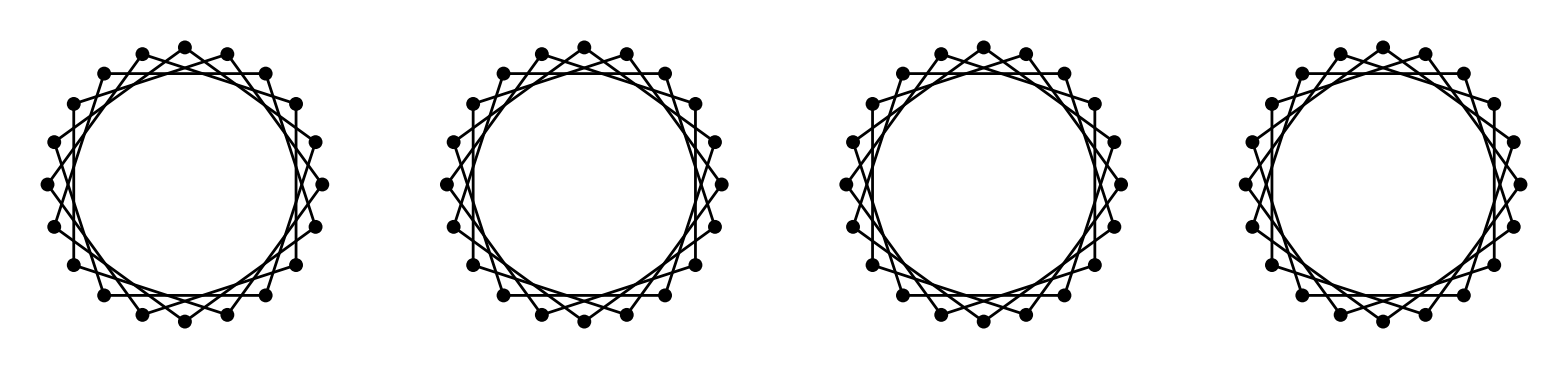

```mathematica
ShowGraphArray[NestList[SpringEmbedding,Combinatorica`CirculantGraph[20,4],3]]
```

### 1.2.3 Generating Graphs

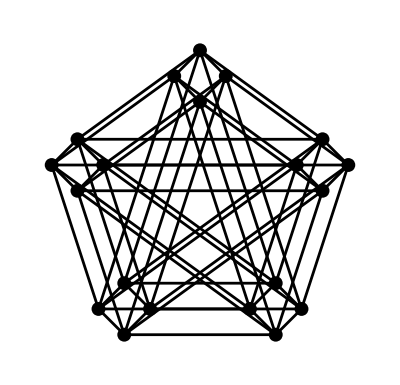

```mathematica
ShowGraph[GraphProduct[Cycle[4],CompleteGraph[5]]]
```

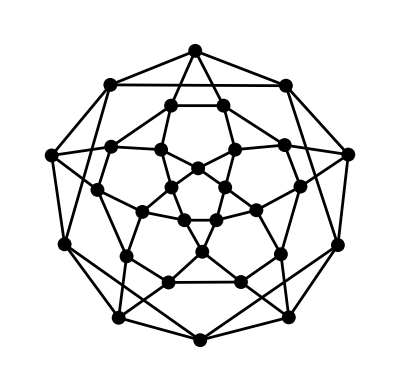

```mathematica
ShowGraph[LineGraph[DodecahedralGraph]]
```

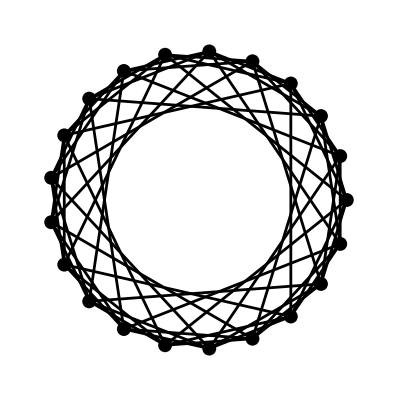

```mathematica
ShowGraph[CirculantGraph[21,RandomKSubset[Range[10],3]]]
```

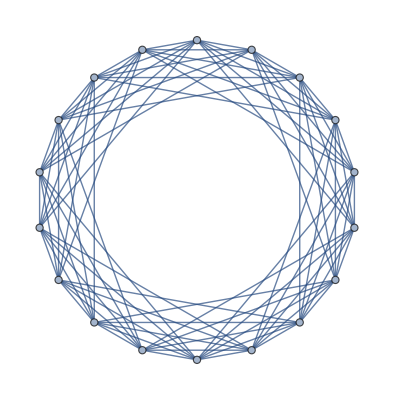

```mathematica
HararyGraph[10,18]
```

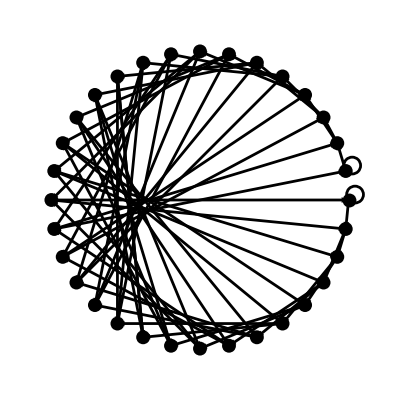

```mathematica
ShowGraph[DeBruijnGraph[2,5]]
```

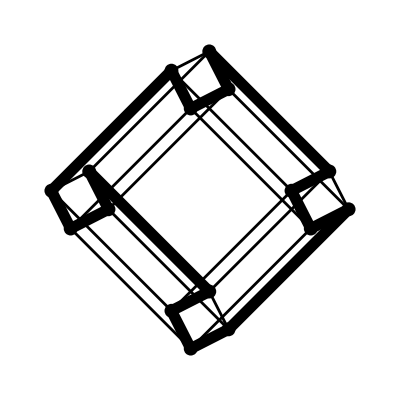

```mathematica
ShowGraph[Highlight[Hypercube[4],{Partition[HamiltonianCycle[Hypercube[4]],2,1]}]]
```

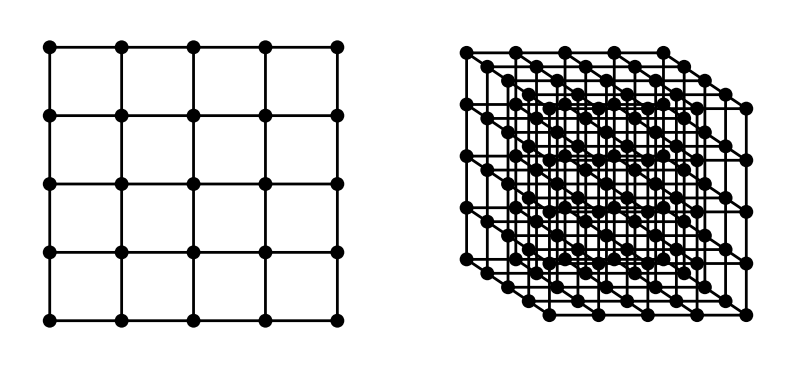

```mathematica
ShowGraphArray[{GridGraph[5,5],GridGraph[5,5,5]}]
```

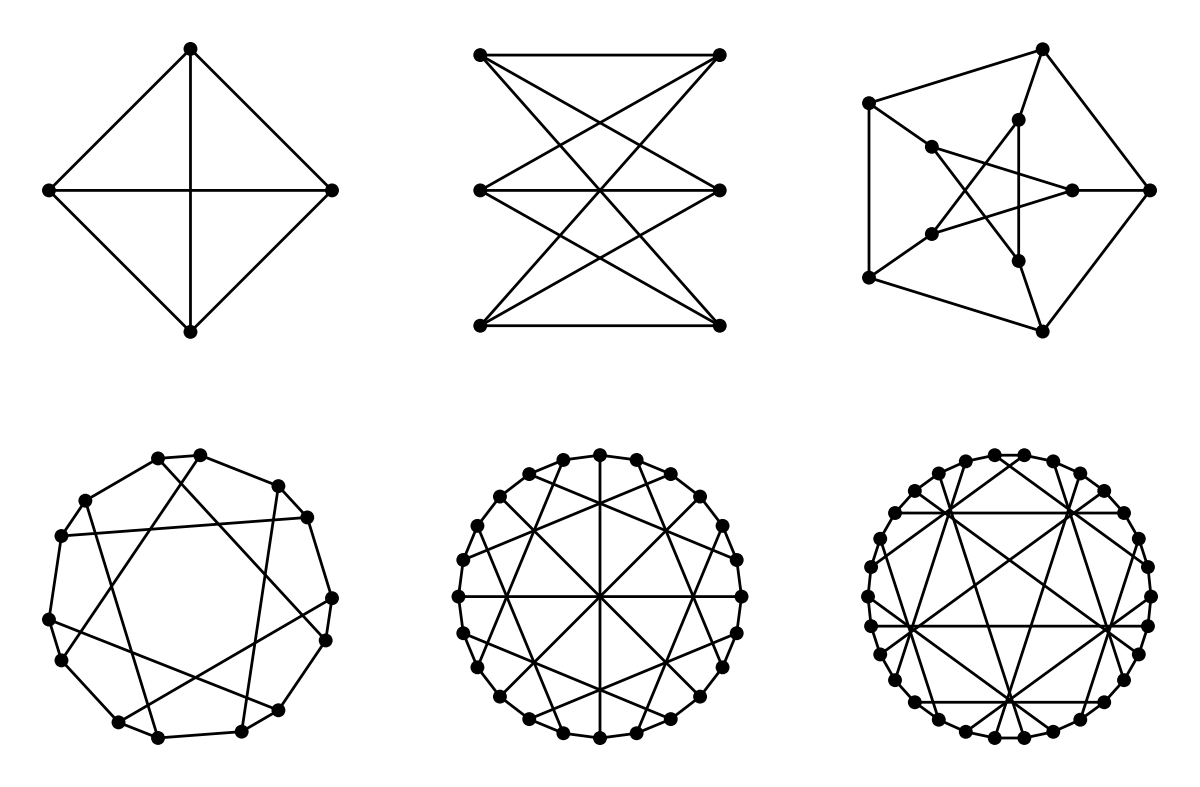

```mathematica
ShowGraphArray[Partition[Table[CageGraph[g],{g,3,8}],3]]
```

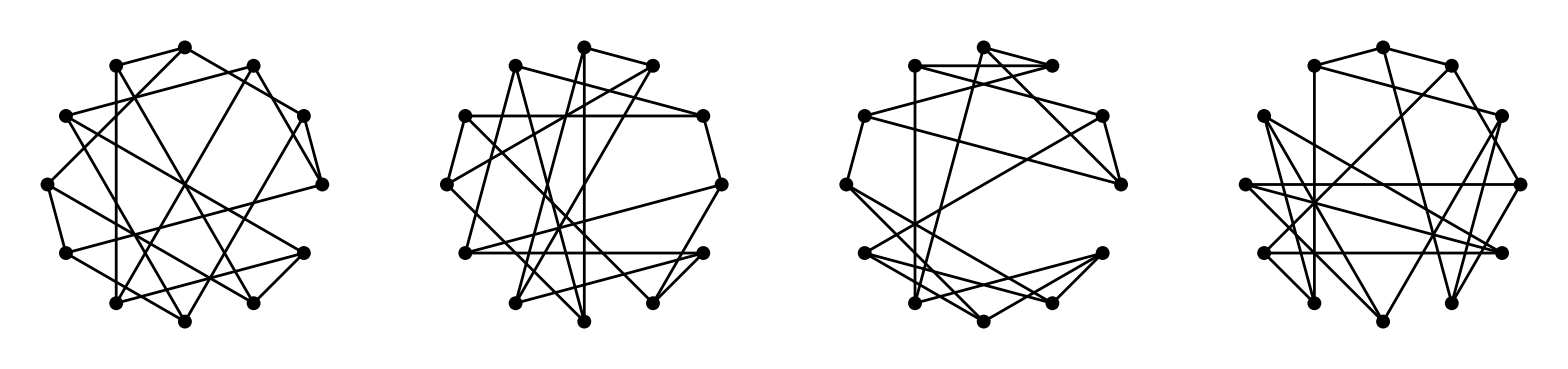

```mathematica
ShowGraphArray[gt=Table[RegularGraph[3,12],{4}]]
```

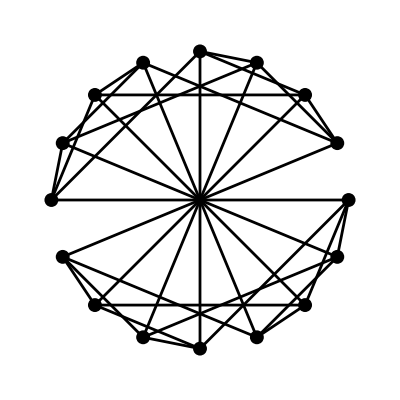

```mathematica
ShowGraph[g=MakeGraph[Strings[{0,1},4],Apply[Plus,Map[Abs,(#1-#2)]]==1&,Type->Undirected]]
```

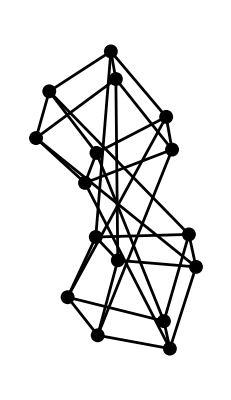

```mathematica
ShowGraph[SpringEmbedding[g,50]]
```

### 1.2.4 Properties of Graphs

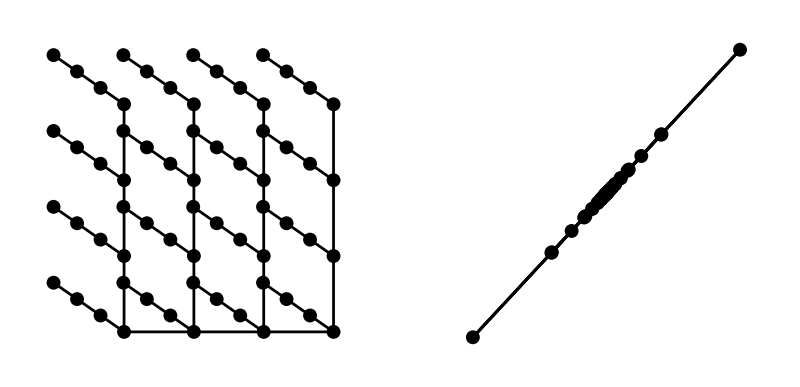

```mathematica
h=BreadthFirstTraversal[g=GridGraph[4,4,4],1,Tree];
ShowGraphArray[{h,SpringEmbedding[h,100]}]
```

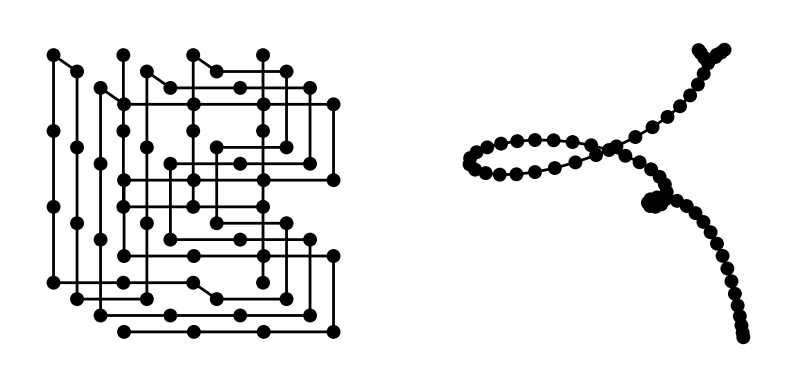

```mathematica
h=DepthFirstTraversal[g,1,Tree];
ShowGraphArray[{h,SpringEmbedding[h,100]}]
```

```mathematica
ConnectedQ[DeleteEdge[Star[10],{1,10}]]
```

False

```mathematica
Length[ConnectedComponents[InduceSubgraph[GridGraph[20,20],RandomSubset[400]]]]
```

32

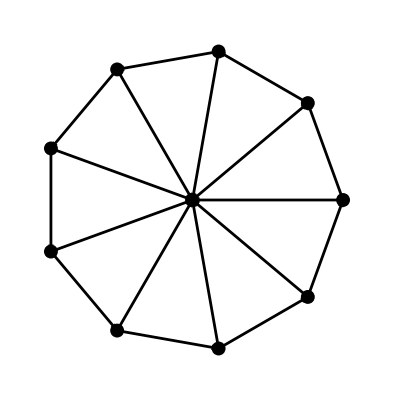

```mathematica
ShowGraph[OrientGraph[Wheel[10]]]
```

```mathematica
BiconnectedComponents[RealizeDegreeSequence[{4,4,3,3,3,2,1}]]
```

{{2,7},{1,2,3,4,5,6}}

```mathematica
BiconnectedComponents[RealizeDegreeSequence[{4,4,3,3,3,2,1}]]
```

{{2,7},{1,2,3,4,5,6}}

```mathematica
ArticulationVertices[Star[10]]
```

{10}

```mathematica
VertexConnectivity[Wheel[10]]
```

3

```mathematica
EdgeConnectivity[CompleteGraph[3,4]]
```

3

```mathematica
AcyclicQ[RandomGraph[100,0.5,Type->Directed]]
```

False

```mathematica
EulerianCycle[CompleteGraph[4,4]]
```

{7,2,8,1,5,4,6,3,7,4,8,3,5,2,6,1,7}

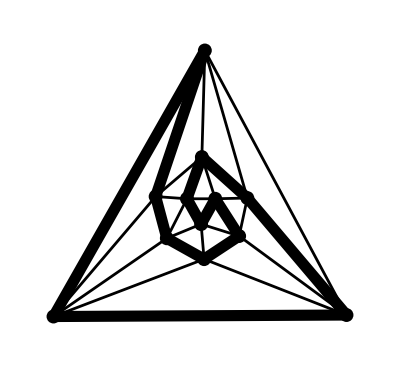

```mathematica
c=Partition[HamiltonianCycle[g=IcosahedralGraph],2,1];
ShowGraph[ Highlight[g,{c}]]
```

⁃Graph:<29,10,Undirected>⁃

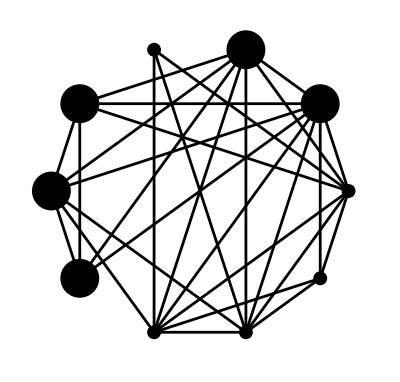

```mathematica
g=RandomGraph[10,0.7]
ShowGraph[Highlight[g,{MaximumClique[g]}]]
```

### 1.2.5 Algorithmic Graph Theory

```mathematica
ManhattanDistance[{2,7},{1,8}]
```

2

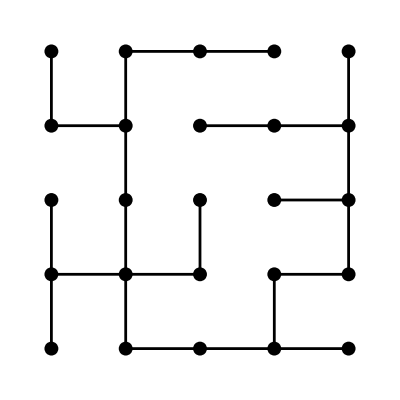

```mathematica
g=SetEdgeWeights[GridGraph[5,5]];
ShowGraph[ShortestPathSpanningTree[g,1]]
```

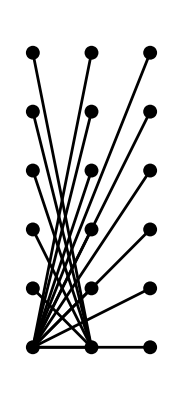

```mathematica
ShowGraph[MinimumSpanningTree[CompleteGraph[6,6,6]]]
```

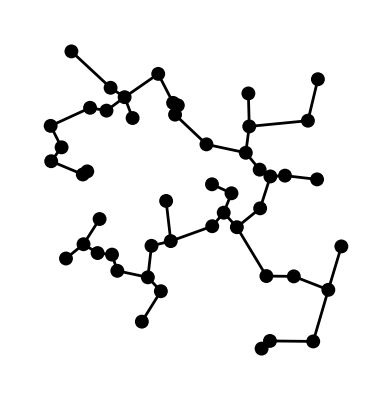

```mathematica
g=SetEdgeWeights[RandomVertices[CompleteGraph[50]],WeightingFunction->Euclidean];
ShowGraph[MinimumSpanningTree[g]]
```

```mathematica
NumberOfSpanningTrees[CompleteGraph[10]]
```

100000000

```mathematica
NetworkFlow[CompleteGraph[7],1,7]
```

6

```mathematica
NetworkFlow[CompleteGraph[7],1,7,Edge]
```

{{{1,2},1},{{1,3},1},{{1,4},1},{{1,5},1},{{1,6},1},{{1,7},1},{{2,7},1},{{3,7},1},{{4,7},1},{{5,7},1},{{6,7},1}}

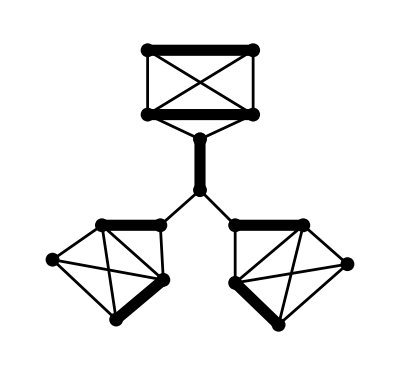

```mathematica
ShowGraph[Highlight[g=NoPerfectMatchingGraph,{MaximalMatching[g]}]]
```

```mathematica
g=InduceSubgraph[GridGraph[20,20],RandomSubset[400]];
{Length[BipartiteMatching[g]],Length[MaximalMatching[g]]}
```

{87,80}

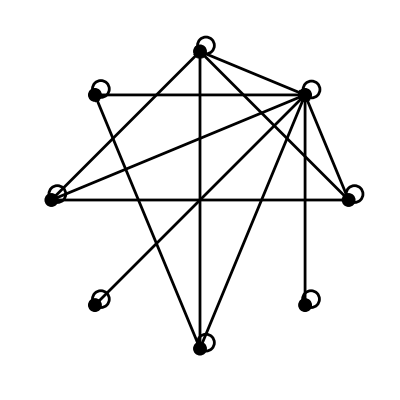

```mathematica
ShowGraph[g=MakeGraph[Range[8],(Mod[#1,#2]==0)&],VertexNumber->True]
```

```mathematica
PartialOrderQ[g]
```

True

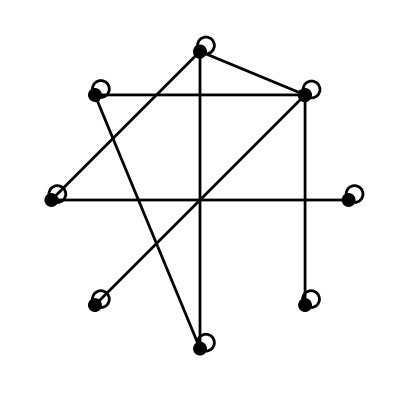

```mathematica
ShowGraph[TransitiveReduction[g],VertexNumber->True]
```

```mathematica
ShowGraph[g=MakeGraph[Range[8],Divisible[#1,#2]&],VertexNumber->True]
```

-Graphics-

```mathematica
PartialOrderQ[g]
```

True

```mathematica
ShowGraph[TransitiveReduction[g],VertexNumber->True]
```

-Graphics-

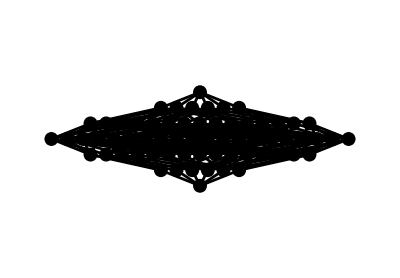

```mathematica
ShowGraph[HasseDiagram[MakeGraph[Subsets[6],((Intersection[#2,#1]===#1)&&(#1!=#2))&]]]
```

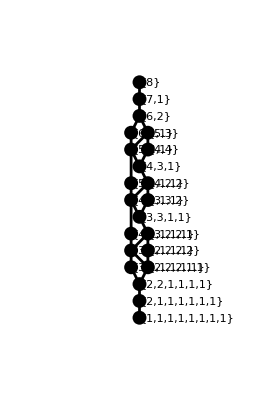

```mathematica
ShowGraph[DominationLattice[8,VertexLabel->True],PlotRange->0.25]
```

```mathematica
Map[PlanarQ,{CubicalGraph,DodecahedralGraph,OctahedralGraph,TetrahedralGraph,IcosahedralGraph}]
```

{True,True,True,True,True}

## 1.3 Combinatorica Conversion Guide

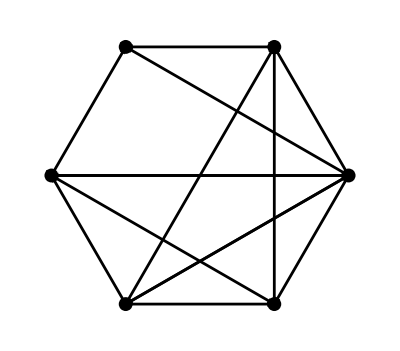

```mathematica
ShowGraph[g=RandomGraph[6,0.5,Type->Directed],VertexNumber->True]
```

```mathematica
{Length[g],g[[3]]}
```

{3,EdgeDirection→True}

```mathematica
AddEdge[g,{1,2}]
```

⁃Graph:<15,6,Directed>⁃

```mathematica
AddEdge[g,{2,1},Directed]
```

AddEdge::obsolete: Usage of Directed as a second argument to AddEdge is obsolete.

⁃Graph:<15,6,Directed>⁃

⁃Graph:<5,5,Undirected>⁃

AddEdge::obsolete: Usage of Directed as a second argument to AddEdge is obsolete.

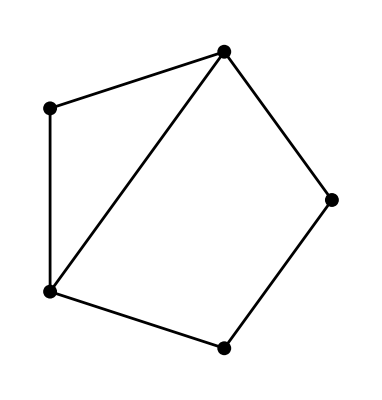

```mathematica
g=Cycle[5]
ShowGraph[AddEdge[g,{1,3},Directed]]
```

```mathematica
h=ChangeEdges[g,{{1,2},{2,3}}]
```

⁃Graph:<2,5,Undirected>⁃

```mathematica
m=ToAdjacencyMatrix[g]
```

{{0,1,0,0,1},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{1,0,0,1,0}}

```mathematica
Edges[FromAdjacencyMatrix[m]]
```

{{1,2},{1,5},{2,3},{3,4},{4,5}}

```mathematica
CircularEmbedding[5]
```

{{{0.309017,0.951057}},{{-0.809017,0.587785}},{{-0.809017,-0.587785}},{{0.309017,-0.951057}},{{1.,0}}}

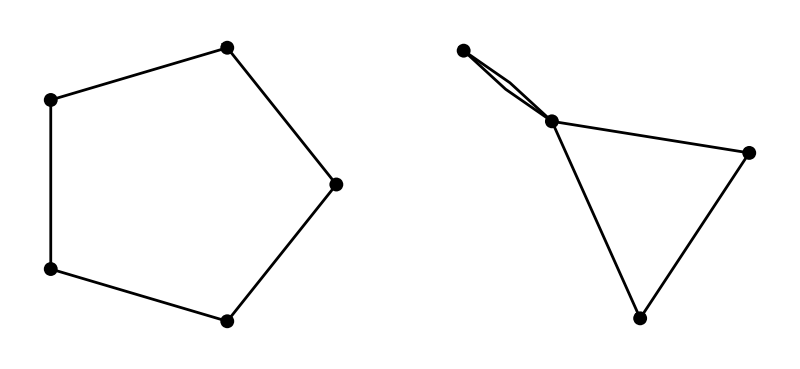

```mathematica
ShowGraphArray[{g=Cycle[5],Contract[g,{1,3}]},VertexNumber->True]
```

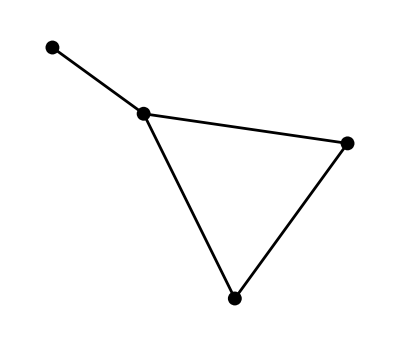

```mathematica
ShowGraph[MakeSimple[Contract[g,{1,3}]]]
```

```mathematica
DeleteCycle[Cycle[5],{1,2,3,4,5,1},Directed]
```

DeleteCycle::obsolete: Usage of Directed as a second argument to DeleteCycle is obsolete.

⁃Graph:<0,5,Undirected>⁃

```mathematica
DeleteEdge[Cycle[5],{1,2},Directed]
```

DeleteEdge::obsolete: Usage of Directed as a second argument to DeleteEdge is obsolete.

⁃Graph:<4,5,Undirected>⁃

```mathematica
Edges[g]
```

{{1,2},{2,3},{3,4},{4,5},{1,5}}

```mathematica
ToAdjacencyMatrix[g]
```

{{0,1,0,0,1},{1,0,1,0,0},{0,1,0,1,0},{0,0,1,0,1},{1,0,0,1,0}}

```mathematica
EulerianCycle[CompleteGraph[5]]
```

{2,3,1,4,5,3,4,2,5,1,2}

```mathematica
EulerianQ[CompleteGraph[5]]
```

True

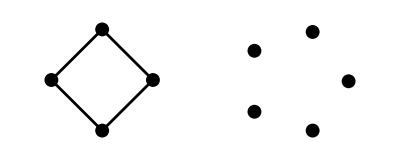

```mathematica
ShowGraph[AddVertices[Cycle[4],5]]
```

```mathematica
FindCycle[Cycle[5],Directed]
```

FindCycle::obsolete: Usage of Directed as a second argument to FindCycle is obsolete.

{5,1,2,3,4,5}

```mathematica
{GrayCode[{1,2,3}],GrayCodeSubsets[{1,2,3}]}//ColumnForm
```

{{},{3},{2,3},{2},{1,2},{1,2,3},{1,3},{1}}
{{},{3},{2,3},{2},{1,2},{1,2,3},{1,3},{1}}

```mathematica
g=SetEdgeWeights[GridGraph[3,2],WeightingFunction->RandomInteger,WeightRange->{1,148}]
```

⁃Graph:<7,6,Undirected>⁃

```mathematica
f=NetworkFlow[g,1,6,Edge]
```

{{{1,2},95},{{2,3},31},{{2,5},64},{{3,6},31},{{5,6},64}}

```mathematica
NetworkFlowEdges[g,1,6]//TableForm
```

1
2 | 95
2
3 | 31
2
5 | 64
3
6 | 31
5
6 | 64

```mathematica
{e,v}={Map[First,f],Map[Last,f]};
ToAdjacencyMatrix[SetEdgeWeights[FromUnorderedPairs[e],v],EdgeWeight]/. Infinity->0//TableForm
```

0 | 95 | 0 | 0 | 0 | 0
95 | 0 | 31 | 0 | 64 | 0
0 | 31 | 0 | 0 | 0 | 31
0 | 0 | 0 | 0 | 0 | 0
0 | 64 | 0 | 0 | 0 | 64
0 | 0 | 31 | 0 | 64 | 0

```mathematica
?NthPermutation
```

```mathematica
Clear[a,b,c,d,e];UnrankPermutation[10,{a,b,c,d,e}]
```

{a,c,e,b,d}

```mathematica
Clear[m,x];
OrbitInventory[CycleIndex[CyclicGroup[8],x],x,m]
```

m/2+m^2/4+m^4/8+m^8/8

```mathematica
DihedralGroup[4]
```

{{1,2,3,4},{4,1,2,3},{3,4,1,2},{2,3,4,1},{4,3,2,1},{3,2,1,4},{2,1,4,3},{1,4,3,2}}

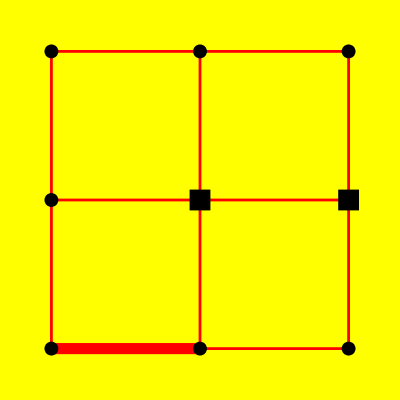

```mathematica
ShowGraph[GridGraph[3,3],{{{1,2},EdgeStyle->Thick},{5,6,VertexStyle->Box[Large]}},EdgeColor->Red,Background->Yellow]
```